InterpolatingFunction::dmval: Input value {-0.999918} lies outside the range of data in the interpolating function. Extrapolation will be used.

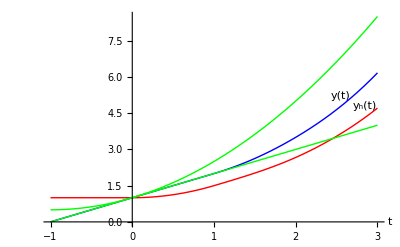

```mathematica
ClearAll;
g[x_[t_]]:=x'[t]-x[t-1];
sol1:=NDSolve[{g[x[t]]==0,x[t/;t≤0]==1+t},x,{t,0,3}];
sol2:=NDSolve[{g[x[t]]==0,x[t/;t≤0]==1},x,{t,0,3}];
p1:=Plot[Evaluate[x[t]/.sol1],{t,-1,3},PlotStyle->Red];
p2:=Plot[Evaluate[x[t]/.sol2],{t,-1,3},PlotStyle->Blue];
p3:=Plot[1+t,{t,-1,3},PlotStyle->Green];
p4:=Plot[1+t+t^2/2,{t,-1,3},PlotStyle->Green]
Show[{p1,p2,p3,p4},AxesLabel->{"t",""},Epilog->{Style[Text["y(t)",{2.55,5.2}],12],Style[Text["y_h(t)",{2.85,4.8}],12]},PlotRange->All,AxesOrigin->{0,0}]
```